```mathematica
ShowGraphDFA[δ_,states_List,q0_,q_List]:=Graph[
MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}],
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
EdgeWeight->Last/@Keys[δ],
EdgeLabels->"EdgeWeight",
VertexStyle->Join[{q0->White},Map[(#->Red)&,q]]
]
```

```mathematica
δ=Association[
{1,"a"}->2,
{2,"a"}->4,
{2,"b"}->1,
{3,"a"}->1,
{3,"b"}->4,
{4,"a"}->4,
{4,"b"}->4
];
```

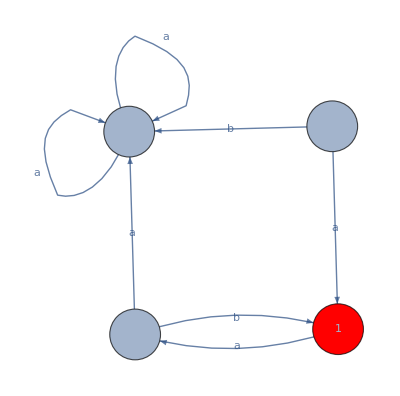

```mathematica
ShowGraphDFA[δ,{1,2,3,4},1,{1}]
```

Primero hay que sacar quienes van hacia 1 y como llegan a este

```mathematica
Select[δ,#==1&]
```

<|{2,b}→1,{3,a}→1|>

```mathematica
q1 = "ϵ + q2b + q3a"
```

ϵ + q2b + q3a

```mathematica
q2 = "q1a"
```

q1a

```mathematica
q3 = "q1b"
```

q1b

```mathematica
q4 = "q2a + q4a + q4b"
```

q2a + q4a + q4b

```mathematica
newExpression = StringReplace[q1, "q2" ->  q2]
```

ϵ + q1ab + q3a

```mathematica
newExpression =StringReplace[newExpression, "q3" ->  q3]
```

ϵ + q1ab + q1ba

```mathematica
newExpression = StringReplace[newExpression, "q3" ->  q3]
```

ϵ + q1ab + q1ba

```mathematica
newExpression = StringReplace[newExpression, "q1" ->  "qf "]
```

ϵ + qf ab + qf ba

```mathematica
simplifiedExpression = Collect[ToExpression[newExpression],qf]
```

(ab+ba) qf+ϵ

## Pregunta 1 Examen 1